Rorschach mask animations projected over 3D surfaces
by Anton Antonov
MathematicaForPrediction at WordPress
MathematicaForPrediction at GitHub
April 2022

## Version 0.3

## Introduction

In this notebook we show a method to make animations of Rorschach images and project those animations over 3D surfaces. The work is inspired by the visual effects of Rorschach's mask in the 2009 movie "Watchmen".

See the gallery "Attempts to recreate Rorschach's mask" for examples.

The following flow chart summarizes the "creation loop."

```mathematica
plFlowChart=;
```

```mathematica
Show[plFlowChart,ImageSize->1600] (*click on the output for full-size chart*)
```

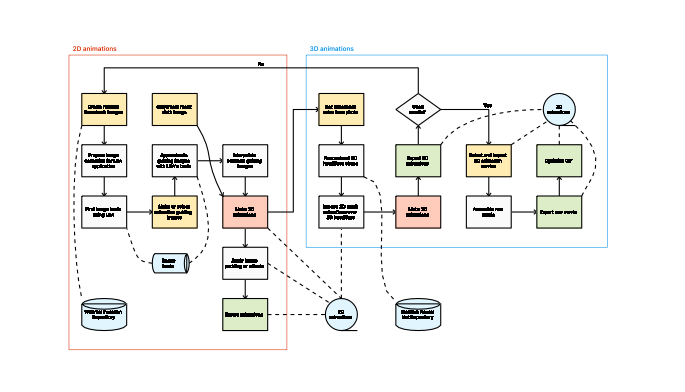
```mathematica
-Graphics-https://community.wolfram.com//c/portal/getImageAttachment?filename=flowchart.jpg&userId=20103Nonehttps://community.wolfram.com//c/portal/getImageAttachment?filename=flowchart.jpg&userId=20103HyperlinkActionRecycledHyperlinkActive
```

The workflow has two main parts:

Making of 2D Rorschach animations

Imposing the 2D images over 3D (head) surfaces

Remark: More detailed explanations will be added in the subsequent versions of the notebook.

## Mask cloth

Here we get a cloth texture image and make a wallpaper with it. (Upon that wallpaper the animations are overlaid below.)

```mathematica
clothOriginal=-Graphics- // ImageAdjust;
```

```mathematica
cloth=ColorReplace[clothOriginal,Black->GrayLevel[0.8],0.65];
clothSq=ImageAssemble[{cloth,ImageReflect[cloth,Left->Right]}];
clothSq=ImageAssemble[{{clothSq},{ImageReflect[clothSq,Top->Bottom]}}];
clothFine=ImageAssemble@Table[clothSq,{5},{5}];
cloth=ImageAssemble@Table[clothSq,{2},{2}];
```

```mathematica
clothSepia=ImageEffect[cloth,"Sepia"];
```

```mathematica
ImageCollage[{cloth,clothFine,clothSepia},Method->"Rows",ImageSize->Medium,ImagePadding->5,Background->LightBlue]
```

## 2D Rorschach animations

In this section we do the following steps:

Generate training Rorschach images

Using Wolfram Function Repository functions RandomScribble or RandomRorschach.

Apply Latent Semantic Analysis (LSA) workflows and extract image topics.

The image topics make an image basis that can be used to approximated other images. See [AA2 and AA5 for details.]

Generate or obtain animation guiding images.

Interpolate between animation guiding images.

The interpolation is done by interpolating between the image basis vectors.

Make animations

Apply image effects

### Get data

Here we generate the training images data. (We experiment with small image sizes, and we get good results we large image sizes.)

```mathematica
SeedRandom[902];
aRes=PrepareImageData["NumberOfImages"->700,ImageSize->200,"Dilation"->False,"Generator"->Hold[ResourceFunction["RandomScribble"]["NumberOfStrokes"->RandomChoice[{10,2,2}->{RandomInteger[{5,20}],{12,40}, {20,16}}],"RotationAngle"->RandomChoice[{Automatic,RandomReal[{0,π},3]}],"OrderedStrokePoints"->False,"ConnectingFunction"->FilledCurve@*BezierCurve,ColorFunction->(Black&),ImageSize->Small]]];
```

```mathematica
aDImages=aRes["Images"];
aDImageVecs=aRes["ImageVectors"];
```

Remark: The function PrepareImageData is from the package [AAp1].

### Apply LSA

Here we apply LSA dimension reduction. (See [AA1-AA5].)

```mathematica
AbsoluteTiming[
lsaObj=DimensionReductionWithLSA[aDImageVecs];
]
```

Get the image basis and show a sample:

```mathematica
aLSABasis=GetImageBasis[lsaObj,aDImages];
RandomSample[aLSABasis["ImageBasis"],4]
```

### Make animation through path

Here we sample the training images in order to get the animation guiding images:

```mathematica
(*SeedRandom[781];
aPath=Sort[RandomSample[aDImages,9]]*)
```

Alternatively, we create animation guiding images on the spot:

```mathematica
SeedRandom[78];
aPath=Sort[Association@Table[i->ColorNegate[ResourceFunction["RandomRorschach"]["NumberOfStrokes"->RandomChoice[{10,2,2}->{RandomInteger[{5,20}],{12,40}, {20,16}}],"RotationAngle"->RandomChoice[{Automatic,RandomReal[{0,π},3]}],"OrderedStrokePoints"->RandomChoice[{False,True}],"ConnectingFunction"->FilledCurve@*BezierCurve,ColorFunction->(Black&)]],{i,9}]];
aPath
```

```mathematica
(*ImageCollage[Values[aPath],Method->"Grid",Background->LightBlue,ImagePadding->4]*)
```

```mathematica
AbsoluteTiming[
aSampleCoeff=Map[RepresentImage[lsaObj,aDImages⟦1⟧,#]&,aPath];
]
Length[aSampleCoeff]
```

```mathematica
AbsoluteTiming[
lsCoeffList=Map[InterpolatedCoefficientMutation[#⟦1⟧,#⟦2⟧,100]&,Partition[Append[Values@aSampleCoeff,aSampleCoeff⟦1⟧],2,1]];
lsCoeffList=Flatten[lsCoeffList,1];
]
Dimensions[lsCoeffList]
```

```mathematica
matH=SparseArray[aLSABasis["H"]];
```

### Rough-looking approximations

```mathematica
AbsoluteTiming[
lsMotionRorschachs=
ParallelMap[(
vecRepresentation=#.matH;
ColorNegate@Dilation[#,0.3]&@Image[Clip[#,{0.45,1},{0,1}]&@Rescale[Partition[vecRepresentation,ImageDimensions[aDImages⟦1⟧]⟦1⟧]]])&,
lsCoeffList,Method->Automatic];
]
```

```mathematica
(*ListAnimate[lsMotionRorschachs]*)
```

### OilPaiting effect

Here we redo the image manipulation with additional binarization in order to get "inkblot look" after applying "OilPainting" effect.

```mathematica
AbsoluteTiming[
lsMotionRorschachsForOil=
ParallelMap[(
vecRepresentation=#.matH;
ColorNegate@Dilation[#,0.3]&@Image[Unitize@Clip[#,{0.55,1},{0,1}]&@Rescale[Partition[vecRepresentation,ImageDimensions[aDImages⟦1⟧]⟦1⟧]]])&,
lsCoeffList,Method->Automatic];
]
```

```mathematica
AbsoluteTiming[
lsMotionRorschachsOil=ParallelMap[ImageEffect[#,"OilPainting"]&,lsMotionRorschachsForOil];
]
```

### Over (non-sepia) cloth

In this sub-section we place the animation images over the mask cloth image derived above.

```mathematica
clothSepia2=ImageResize[clothFine,ImageDimensions[lsMotionRorschachs⟦1⟧]];
```

```mathematica
AbsoluteTiming[
lsMotionRorschachs2=ParallelMap[ImageMultiply[clothSepia2,#]&,lsMotionRorschachs];
]
```

```mathematica
AbsoluteTiming[
lsMotionRorschachs3=ParallelMap[ImageMultiply[clothSepia2,#]&,lsMotionRorschachsOil];
]
```

```mathematica
ListAnimate[lsMotionRorschachs2]
```

### Head-mask padding

In order to produce more "centered" animations on the reconstructed face we pad the images of the animation:

```mathematica
AbsoluteTiming[
padSize=Round[N@ImageDimensions[lsMotionRorschachs⟦1⟧]⟦1⟧/(3)];
lsPaddedMotionRorschachs=ParallelMap[ImagePad[#,padSize,White]&,lsMotionRorschachs];
]
```

## Export 2D animations

In this section we export the animations and a collage of the guiding images.

```mathematica
AbsoluteTiming[
Export[FileNameJoin[{NotebookDirectory[],"AnimatedGIFs","MotionRorschach-"<>StringReplace[DateString["ISODateTime"],":"->"-"]<>".mp4"}],lsMotionRorschachs,"MP4","DisplayDurations"->0.05];
]
```

```mathematica
AbsoluteTiming[
Export[FileNameJoin[{NotebookDirectory[],"AnimatedGIFs","MotionRorschach-guiding-images"<>StringReplace[DateString["ISODateTime"],":"->"-"]<>".jpg"}],ImageCollage[ColorNegate/@Values[aPath],"Stretch",Method->"Grid",Background->LightBlue,ImagePadding->3],"JPEG"];
]
```

{0.292795,Null}

## Facial 3D Reconstruction

In this section we follow the code an explanations in "Facial 3D Reconstruction".

```mathematica
net=NetModel["Unguided Volumetric Regression Net for 3D Face Reconstruction"]
```

NetChain[<>]

```mathematica
face = -Graphics-;
```

```mathematica
face3D=Image3D[net[face]];
```

```mathematica
reconstruction=Blur@ImageReflect[ImageResize[face3D,Append[ImageDimensions[face],105]],Bottom->Front];
```

```mathematica
coloredSlices=Map[SetAlphaChannel[face,#]&,Image3DSlices[reconstruction,All,2]];
```

```mathematica
(*ImageReflect[Image3D[coloredSlices,ViewPoint->{1,-2,0},ViewAngle->20 °,ImageSize->300],Bottom->Front]*)
```

Remark: Of course, we can also use, say, photos of Jackie Earle Haley portraying Rorschach in the movie "Watchmen" (2009). For reproducibility purposes we use the photo in the linked article.

## Impose Rorschach animation over face

In this section we impose the 2D animation images over the 3D reconstructed face.

### Single image

In this sub-section we show the process of imposing a single animation image.

```mathematica
cloth2=ImageResize[cloth,ImageDimensions[face]];
```

```mathematica
img2=ImageResize[lsPaddedMotionRorschachs⟦400⟧,ImageDimensions[face]];
img3=ImageMultiply[cloth2,img2];
lsRoschachSlices=Map[SetAlphaChannel[img3,#]&,Image3DSlices[reconstruction,All,2]];
```

```mathematica
Rasterize@ImageReflect[Image3D[lsRoschachSlices,ViewPoint->{-1.6,-2,0},ViewAngle->20 °,ImageSize->300,ColorFunction->GrayLevel,Background->LightGreen],Bottom->Front]
```

-Graphics-

### Animation

In this sub-section we apply the imposing for all animation images.

```mathematica
cloth2=ImageResize[cloth,ImageDimensions[face]];
```

```mathematica
AbsoluteTiming[
ls3DRorschachs=
Table[(
img2=ImageResize[img,ImageDimensions[face]];
img3=ImageMultiply[cloth2,img2];
lsRoschachSlices=Map[SetAlphaChannel[img3,#]&,Image3DSlices[reconstruction,All,2]];
ImageReflect[Image3D[lsRoschachSlices,ViewPoint->{-1.6,-2,0},ViewAngle->20Degree,ImageSize->300,ColorFunction->GrayLevel,Background->LightGreen],Bottom->Front]),
{img,lsMotionRorschachs⟦1;;-1;;2⟧}
];
]
```

{70.0789,Null}

```mathematica
AbsoluteTiming[
ls3DRorschachs2=ParallelMap[ImageRotate[#,{-π/3,Append[Most@ImageDimensions[#]/2,1]}]&,ls3DRorschachs⟦1;;12⟧];
]
```

{12.0906,Null}

```mathematica
lsAngles=Table[-(i-1)*π/(3.2*360),{i,Length[ls3DRorschachs]}];
Length[lsAngles]
```

450

```mathematica
AbsoluteTiming[
ls3DRorschachs4=MapThread[ImageRotate[#1,#2]&,{ls3DRorschachs,lsAngles}];
]
```

{97.7362,Null}

## Export 3D animations

Here we export the 3D animation:

```mathematica
AbsoluteTiming[
Export[FileNameJoin[{NotebookDirectory[],"AnimatedGIFs","HeadRorschach-"<>StringReplace[DateString["ISODateTime"],":"->"-"]<>".mp4"}],ls3DRorschachs4,"MP4","DisplayDurations"->0.05];
]
```

## Multiple Rorschach heads in a row

In this section we get (a selection of) GIF animations and assemble them into one movie. The imported movie are expected to have the same number of frames. The corresponding frames are combined into one frame (in the new movie.)

Get the “custom rotation” batch of images:

```mathematica
lsFileNames=Sort@FileNames["HeadRorschach-2022-04-24T12*gif",FileNameJoin[{NotebookDirectory[],"AnimatedGIFs"}]];
Length[lsFileNames]
```

3

Import the movie files and show the number of frames per file:

```mathematica
AbsoluteTiming[
grs=Import[#]&/@lsFileNames;
]
Length/@grs
```

{1.36481,Null}

{450,450,450}

Assemble corresponding frames into one image:

```mathematica
Block[{c=40},
lsImgsMulti=MapThread[(d=ImageDimensions[#1];ImageAssemble[ImageTake[#,All,{c,-c}]&/@{#1,ImageResize[#2,d],ImageResize[#3,d]}])&,grs];
]
Length[lsImgsMulti]
```

450

Export the assembled frames into a GIF:

```mathematica
AbsoluteTiming[
resFileName=Export[FileNameJoin[{FileNameJoin[{NotebookDirectory[],"AnimatedGIFs"}],"Rorschach-heads-row-"<>StringReplace[DateString[Now,"ISODateTime"],":"->"-"]<>".gif"}],lsImgsMulti,"GIF","AnimationRepetitions"->Infinity,"DisplayDurations"->0.025];
]
```

{7.89872,Null}

Check assembling result:

```mathematica
(*ListAnimate[lsImgsMulti]*)
```

## Going further

The process above can modified or extended in several ways:

Different training images

Different animation guiding images

Additional image re-styling

### Using random mandalas

We can use random mandalas [AAf3] instead of random Rorschach images [AAf1]. See for example this animation: https://imgur.com/ygLurTM .

### Guiding through the original Rorschach images

I experimented with using the original Rorschach images as animation guiding images. (The results were not particularly better or more interesting looking.)

### Using image restyling

Also, we can use ImageRestyle to impose certain more "realistic" look into the derived animations. (Or any other style.)

Here is an example with imposing the style of the original Rorschach images: https://imgur.com/UWv4CUG .

## Setup

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/Misc/LSAMonForImageCollections.m"]
```

## References

[AA1] Anton Antonov, "A monad for Latent Semantic Analysis workflows", (2019), Wolfram Community.

[AA2] Anton Antonov, "LSA methods comparison over random mandalas deconstruction -- WL", (2022), Wolfram Community.

[AA3] Anton Antonov, "Bethlehem stars: classifying randomly generated mandalas", (2020), Wolfram Community.

[AA4] Anton Antonov, "[LiVE] Latent Semantic Analysis Workflows (WL Live-Stream Series)", (2019), Wolfram Community.

[AA5] Anton Antonov, "Re-exploring the structure of Chinese character images​", (2022), Wolfram Community.

[AAp1] Anton Antonov, LSAMon for Image Collections Mathematica package, (2022), MathematicaForPrediction at GitHub.

[AAf1] Anton Antonov, "RandomRorschach", (2022), Wolfram Function Repository.

[AAf2] Anton Antonov, "RandomScribble", (2021), Wolfram Function Repository.

[AAf3] Anton Antonov, "RandomMandala", (2019), Wolfram Function Repository.